```mathematica
(*
LandauTransition-PaperDataAnalysis.nb
Bryan Daniels
2021.10.6 NOTE: Most analysis is now being done in python.  See landau-bee-data-analysis.ipynb.  This mathematica notebook is still being used to test the landau fitting and to create the transition dimension plots that show individual genes.
*)
```

### Define distribution

```mathematica
LandauTransitionDistributionRelativeLogPDF[x_,mu_,J_,nu_,c_,d_]:=-(1/2)(x-mu).J.(x-mu)-((c-1)/2)(nu.J.nu)((x-mu).nu)^2-(d/4)(nu.J.nu)^2((x-mu).nu)^4
```

```mathematica
(*for now we'll restrict nu to be along an eigenvector of J---the index of nu in Jvals is nuIndex*)logNormalizationDiagonal[Jvals_,nuIndex_,c_,d_]:=((Length[Jvals]-1)/2)Log[2π]+0.5(Log[Jvals[[nuIndex]]]-Plus@@Log[Jvals])+Log[If[c>0,(c ⅇ^(c^2/(8 d)) BesselK[1/4,c^2/(8 d)])/(√2 √(c d Jvals[[nuIndex]])),(ⅇ^(c^2/(8 d)) π (BesselI[-1/4,c^2/(8 d)]+BesselI[1/4,c^2/(8 d)]))/(2 √(-(d Jvals[[nuIndex]])/c))]]
```

```mathematica
(*(Assumes any zeros come at the end of Jvals for nuIndex to work)*)LandauTransitionDistributionLogPDFdiagonal[x_,mu_,Jvals_,Jvecs_,nuIndex_,c_,d_,nuMu_]:=
With[{
J=Transpose[Jvecs].DiagonalMatrix[Jvals].Jvecs,
nu=Jvecs[[nuIndex]]},
LandauTransitionDistributionRelativeLogPDF[x,mu+nuMu nu,J,nu,c,d]-logNormalizationDiagonal[Select[Jvals,#>0&],nuIndex,c,d]
]
```

```mathematica
logNormalizationGaussian[Jvals_]:=(Length[Jvals]/2)Log[2π]+0.5(-Plus@@Log[Jvals])
```

```mathematica
GaussianLogPDFdiagonal[x_,mu_,Jvals_,Jvecs_]:=
With[{
J=Transpose[Jvecs].DiagonalMatrix[Jvals].Jvecs,
nu=Table[1,Length[Jvals]]},
LandauTransitionDistributionRelativeLogPDF[x,mu,J,nu/Norm[nu],1,0]-logNormalizationGaussian[Select[Jvals,#>0&]]
]
```

```mathematica
GaussianRelativeLogPDF[x_,mu_,J_]:=
With[{nu=Table[1,Length[J]]},
LandauTransitionDistributionRelativeLogPDF[x,mu,J,nu/Norm[nu],1,0]
]
```

```mathematica
LandauTransitionDistributionRelativeLogPDFmarginal[x1_,indices_,muFull_,JFullVals_,JFullVecs_,nuIndex_,c_,d_,nuMu_]:=
With[{JFull=Transpose[JFullVecs].DiagonalMatrix[JFullVals].JFullVecs,
nuFull=JFullVecs[[nuIndex]]},
Module[{valsModified,JzeroNu,covZeroNu,covZeroNuMarginal,JzeroNuMarginal},
valsModified=JFullVals;
valsModified[[nuIndex]]=0;
JzeroNu=Transpose[JFullVecs].DiagonalMatrix[valsModified].JFullVecs;
covZeroNu=PseudoInverse[JzeroNu];
covZeroNuMarginal=covZeroNu[[indices,indices]];
JzeroNuMarginal=PseudoInverse[covZeroNuMarginal];
Log[
NIntegrate[
Exp[GaussianRelativeLogPDF[x1,(muFull+nuMu nuFull + eta nuFull)[[indices]],JzeroNuMarginal]]Exp[-((c)/2)(nuFull.JFull.nuFull)eta^2-(d/4)(nuFull.JFull.nuFull)^2 eta^4],{eta,-∞,∞}]
]
]
]
```

### Define Landau algorithm

output of LandauMaxLikelihood : {fitMu, fitVals, fitVecs, fitparams}

```mathematica
LandauMaxLikelihood[dataFull_,numNuMax_:10,dmin_:0.001,flipSignOfVecs_:True]:=
With[
{Jinit=PseudoInverse[Covariance[dataFull](Length[dataFull]-1)/Length[dataFull]],
muInit=Mean[dataFull],
Nsamples=Length[dataFull],
Ncomponents=Length[First[dataFull]]},
With[{
x=dataFull,
(*eigenvalues of J are put in increasing order, with any zeros at the end*)
Jvals=PadRight[Reverse[SingularValueList[Jinit]],Ncomponents],
JvecsUnordered=If[flipSignOfVecs,-1,1]Eigenvectors[Jinit]},
With[{
maxNuIndex=Count[Jvals,val_/;val≠0],
Jvecs=Join[
Reverse[JvecsUnordered[[;;Count[Jvals,val_/;val≠0]]]],
JvecsUnordered[[Count[Jvals,val_/;val≠0]+1;;]]]},
{muInit,Jvals,Jvecs,
Table[
(*Check there's nothing weird going on with imaginary numbers in vecs, at least for c=1,d=1*)
If[Re[-Sum[LandauTransitionDistributionLogPDFdiagonal[x[[i]],muInit,Jvals,Jvecs,nuIndex,1,1,0],{i,1,Nsamples}]]≠Abs[-Sum[LandauTransitionDistributionLogPDFdiagonal[x[[i]],muInit,Jvals,Jvecs,nuIndex,1,1,0],{i,1,Nsamples}]],somethingIsWrong,
(*Do the actual minimization*)
Quiet[
FindMinimum[{-Sum[LandauTransitionDistributionLogPDFdiagonal[x[[i]],muInit,Jvals,Jvecs,nuIndex,c,d ,nuMu],{i,1,Nsamples}]+Sum[GaussianLogPDFdiagonal[x[[i]],muInit,Jvals,Jvecs],{i,1,Nsamples}],{d>dmin}},{{c,1},{d,1},{nuMu,0}}],
{FindMinimum::nrnum,FindMinimum::eit}]],
{nuIndex,1,Min[maxNuIndex,numNuMax]}
]}
]
]
]
```

```mathematica
Index[item_,list_]:=First[FirstPosition[list,item]]
```

### Load bee data

```mathematica
rawdata=Import["/Users/bdaniel6/Dropbox (ASU)/Research/bees/geneExpression/Data/170614/nanostring data with VG protein data.xlsx"]//First;
```

data is indexed by age, bee, then gene

```mathematica
data=Table[Select[rawdata,#[[2]]==age&],{age,{1,3,4,6,10,15}}][[;;,;;,5;;-2]];
```

```mathematica
ages=Intersection[rawdata[[2;;,2]]]
```

{1.,3.,4.,6.,10.,15.}

```mathematica
genes=rawdata[[1,5;;-2]]
```

{4ebp1,AGO1,AGO2,AKH,AKHR,AKT1,Ago3,Aub,Br-c,Chd64,Creb,Dcr1,Def,Def2,Dop1,Dop3,DopR2,E74,E75,EcR,Eth,Ethr,FOXO,Ftz-f1,HR38,HR46,Hbg3,Hex70a,Hymenoptaecin,ILP-2,IRS,InR1,InR2,JHBP-1,JHE,JHEH,Kr-h1,LOC100577942,LOC102655054,LOC406144,LOC409966,LOC410022,LOC412541,LOC413141,LOC413670,LOC724829,LOC726648,LOC726781,LOC726899 GB52437,MRJP-3,MRJP-5,MRJP-9,MRJP1,Malvolio,Mkp3,Mob3,Mtp,NAA35,OA1 or OAR,P110,PDK1,PKG (For),PRM1,PTEN,Rheb,SVP NR2F1,SmG,TOR,TYR1,Tbh,USP (RXR),Vas,cad,dnmt1a,dnmt2,dnmt3,egfr,erk7,hex 110,if,ilp1,mdy,phosphatidylinositol 4 5-bisphosphate 3-kinase catalytic subunit delta isoform,proPO,tdc1,tdc2,ten-M,transferrin 1,vg,vgR,VG protein }

```mathematica
{Length[ages],Length[genes]}
```

{6,91}

```mathematica
Dimensions[data]
```

{6,16,91}

```mathematica
ages
```

{1.,3.,4.,6.,10.,15.}

```mathematica
FindLessThan[lst_,val_]:=First/@Position[Less[#,val]&/@lst,_?(TrueQ)]
```

```mathematica
(*8.25.2018 deal with outlier bee*)
(*outlier=data['4ebp1']>40000*)
nonBadBeesDayFour=FindLessThan[data[[Index[4.,ages],;;,Index["4ebp1",genes]]],40000]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,16}

```mathematica
allBees=Table[i,{i,16}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16}

```mathematica
(*9.5.2018 I'm curious: Is the largest variance dimension on Day 4 still the one with the hexamarins and vg?  Hmm.  No, not obviously.*)
ageDay=4.;
keptDimensionsDay=If[ageDay==4,90,91];
keptBeesDay=If[ageDay==4,nonBadBeesDayFour,allBees];
dataFullDay=Log[data[[Index[ageDay,ages]]]][[keptBeesDay,;;keptDimensionsDay]];JinitDay=PseudoInverse[Covariance[dataFullDay](Length[dataFullDay]-1)/Length[dataFullDay]];
JvalsDay=Join[SingularValueList[JinitDay],Table[0,Dimensions[dataFullDay][[2]]-(Dimensions[dataFullDay][[1]]-1)]];
JvecsDay=Eigenvectors[JinitDay];
```

```mathematica
(*choose eigenvector to look at.  note: smallest eigenvalues correspond to largest variance.*)
vecIndexDay=14;
Print["Jval = ",JvalsDay[[vecIndexDay]]];
vDay=JvecsDay[[vecIndexDay]];
orderingDay=Ordering[-vDay^2];
orderedVecDay=Transpose[{genes[[orderingDay]],Sign[First[vDay[[orderingDay]]]]vDay[[orderingDay]]}];
orderedVecDay[[;;10]]
```

Jval = 0.0264698

{{LOC102655054,0.213398},{Kr-h1,0.161342},{cad,0.159356},{TYR1,0.154677},{Hbg3,0.153254},{E75,0.149248},{InR1,0.142866},{Chd64,0.139606},{transferrin 1,0.13209},{hex 110,0.130976}}

### Define fancy plots

#### playing with colors

```mathematica
Lighter[Darker[Green]]
```

RGBColor[Rational[1, 3], Rational[7, 9], Rational[1, 3]]

```mathematica
Lighter[Lighter[Darker[Yellow]]]
```

RGBColor[Rational[23, 27], Rational[23, 27], Rational[5, 9]]

```mathematica
Lighter[Lighter[Yellow]]
```

RGBColor[1, 1, Rational[5, 9]]

```mathematica
Lighter[Orange]
```

RGBColor[1, 0.6666666666666666, Rational[1, 3]]

```mathematica
Orange
```

RGBColor[1, 0.5, 0]

```mathematica
Lighter[Lighter[Purple]]
```

RGBColor[0.7777777777777778, Rational[5, 9], 0.7777777777777778]

```mathematica
Lighter[Purple]
```

RGBColor[0.6666666666666666, Rational[1, 3], 0.6666666666666666]

```mathematica
Purple
```

RGBColor[0.5, 0, 0.5]

```mathematica
LinearGradientImage[{Purple,Orange}]
```

-Graphics-

```mathematica
LinearGradientImage[{Darker[Purple],Orange}]
```

-Graphics-

```mathematica
LinearGradientImage[{Darker[Lighter[Purple]],Orange}]
```

-Graphics-

```mathematica
LinearGradientImage[{Lighter[Purple],Orange}]
```

-Graphics-

```mathematica
LinearGradientImage[{Lighter[Purple],Lighter[Orange]}]
```

-Graphics-

```mathematica
LinearGradientImage[{Lighter[Lighter[Red]],Orange}]
```

-Graphics-

```mathematica
COLOR1=Lighter[Purple];
COLOR2=Orange;
```

#### plot definitions

```mathematica
(*make plot along single dimension*)
bistableWellPlot[dataFull_,fitMu_,fitVals_,fitVecs_,fitParams_,nuIndex_,projectionVec_,colors_(*,xmaxScale_:10*)]:=
With[
{c=c/.fitParams[[nuIndex]][[2]],
d=d/.fitParams[[nuIndex]][[2]],
nuMu=nuMu/.fitParams[[nuIndex]][[2]],
transformedData=((
#-fitMu
-(nuMu/.fitParams[[nuIndex]][[2]]) fitVecs[[nuIndex]]
)&/@dataFull).projectionVec},
Block[{scale,logymax,yscale,aratio},
aratio=1/5(*1/2*);
scale=(*2022/9/20 try fixed horizontal scale*)
scale=10(*0.8(Max[transformedData]-Min[transformedData])*)(*If[c<0,Sqrt[-xmaxScale c/d/fitVals[[nuIndex]]],Sqrt[xmaxScale c/fitVals[[nuIndex]]]]*);
yscale=2scale aratio ;
logymax=NMaxValue[{LandauTransitionDistributionLogPDFdiagonal[fitMu+nuMu fitVecs[[nuIndex]]+deltax projectionVec,fitMu,fitVals,fitVecs,nuIndex,c,d,nuMu],-scale<deltax<scale},deltax];
(*Print["logymax = ",logymax];*)
Show[
Plot[
yscale Exp[
(*LandauTransitionDistributionLogPDFdiagonal[fitMu,fitMu,fitVals,fitVecs,nuIndex,c,d]-*)LandauTransitionDistributionLogPDFdiagonal[fitMu+nuMu fitVecs[[nuIndex]]+deltax projectionVec,fitMu,fitVals,fitVecs,nuIndex,c,d,nuMu]-logymax
],
{deltax,-scale,scale},Filling->Bottom,Axes->{True,False},PlotRange->{0,1.075yscale}(*{-1.35,1.35}*)],
(*ListPlot[Transpose[{transformedData,ConstantArray[0,Length[dataFull]]}],
PlotStyle->PointSize[0.05]]*)
ScatterPlotColors[transformedData,
colors,
0.3],
PlotRangeClipping->False,
AspectRatio->Automatic(*aratio*),
(*tick spacing*)
Ticks->{Range[-20,20,Log[10]
(*Piecewise[{{0.5,scale<1},{Ceiling[scale/2],scale≥1}}]*)],Automatic},
(*remove tick labels*)TicksStyle->Directive[FontOpacity->0,FontSize->0]
]
]
]
```

```mathematica
bistableWellPlotOneGene[dataFull_,fitMu_,fitVals_,fitVecs_,fitParams_,nuIndex_,geneIndex_,colors_,maxLabelLength_:11,fontSize_:14(*,xmaxScale_:10*)]:=
With[
{c=c/.fitParams[[nuIndex]][[2]],
d=d/.fitParams[[nuIndex]][[2]],
nuMu=nuMu/.fitParams[[nuIndex]][[2]],
data=dataFull[[;;,geneIndex]],
geneMu=fitMu[[geneIndex]]},
Block[{scale,logymax,aratio,yscale},
aratio=1/5;
(*2022/9/20 try fixed horizontal scale*)
scale=5(*(0.8(Max[data]-Min[data])*);
yscale=2scale aratio;
(*DEVELOP*)(**)
logymax=NMaxValue[{LandauTransitionDistributionRelativeLogPDFmarginal[{geneMu+deltax},{geneIndex},fitMu,fitVals,fitVecs,nuIndex,c,d,nuMu],-scale<deltax<scale},deltax,MaxIterations->1];
(**)(*END DEVELOP*)
(*Print["logymax = ",logymax];*)
Show[
Plot[
(*DEVELOP*)(**)
yscale Exp[
LandauTransitionDistributionRelativeLogPDFmarginal[{deltax},{geneIndex},fitMu,fitVals,fitVecs,nuIndex,c,d,nuMu]-logymax],
(**)
(*Exp[-deltax^2],*)
(*END DEVELOP*)
{deltax,
geneMu+nuMu fitVecs[[nuIndex]][[geneIndex]]-scale,geneMu+nuMu fitVecs[[nuIndex]][[geneIndex]]+scale},
Filling->Bottom,Axes->{True,False},PlotRange->{{geneMu+nuMu fitVecs[[nuIndex]][[geneIndex]]-scale,
geneMu+nuMu fitVecs[[nuIndex]][[geneIndex]]+scale},{0,(*1.075*)1.15 yscale}},
AspectRatio->Automatic],
ScatterPlotData1D[dataFull,genes[[geneIndex]],colors,0.12],
(*FrameLabel->{Style[StringTake[genes[[geneIndex]],UpTo[maxLabelLength]],fontSize],None},*)
PlotRangeClipping->False,Frame->{{False,False},{True,False}}
,FrameTicks->{Range[-20,20,Log[10](*tick spacing*)(*Piecewise[{{0.5,scale<1},{Ceiling[scale/2],scale≥1}}]*)],Automatic},
(*remove tick labels*)FrameTicksStyle->Directive[FontOpacity->0,FontSize->0]
]
]
]
```

```mathematica
(*currently repurposed for the 1D case*)
(*old "ball and stick" version*)
ScatterPlotColorsBallAndStick[xList_,yList_,colors_]:=
With[{points=Transpose[{xList,yList}]},Graphics[{PointSize[0.03],Thread[{colors,Point/@points,{Thick,Line[{{#[[1]],0},#}]}&/@points}]},AspectRatio->1/3(*1/GoldenRatio*),Axes->{True,False}]]
```

```mathematica
(*new swarm plot version*)
(*previous version of below had radius=(Max[xList]-Min[xList])/40*)
ScatterPlotColors[xList_,colors_,radius_]:=beeswarmPlot[xList,colors,radius]
```

```mathematica
(*no longer used?*)
ScatterPlotData[dataFull_,gene1_,gene2_,colors_,radius_]:=
Show[
ScatterPlotColors[
dataFull[[;;,Index[gene1,genes]]],dataFull[[;;,Index[gene2,genes]]],
colors,
radius],
FrameLabel->{gene1,gene2},Frame->True,Axes->False]
```

```mathematica
ScatterPlotData1D[dataFull_,gene_,colors_,radius_]:=
Show[
ScatterPlotColors[
dataFull[[;;,Index[gene,genes]]],
colors,
radius],AspectRatio->1/10,Axes->False,PlotRange->{All,{0,1.1}}]
```

```mathematica
(*haven't tested this*)
ScatterPlotData1DBallAndStick[dataFull_,gene_,colors_,height_:0.11]:=
Show[
ScatterPlotColorsBallAndStick[
dataFull[[;;,Index[gene,genes]]],
Table[height,Length[dataFull]],
colors],AspectRatio->1/10,Axes->False,PlotRange->{All,{0,1.1}}]
```

```mathematica
(*Plot bistability along the relevant eigenvector*)
```

```mathematica
bistablePlotEigvec[dataFull_,fitMu_,fitVals_,fitVecs_,fitParams_,nuIndex_,runString_:""]:=
With[
{v=fitVecs[[nuIndex]],
transformedData=((#-fitMu-(nuMu/.fitParams[[nuIndex]][[2]]) fitVecs[[nuIndex]])&/@dataFull).fitVecs[[nuIndex]],
color1=COLOR1,
color2=COLOR2
},
Block[{colors,eigenvectorPlot},
colors=Blend[{{Min[transformedData],color1},{Max[transformedData],color2}},#]&/@transformedData;
(*Blend[{{-Max[Abs[transformedData]],color1},{Max[Abs[transformedData]],color2}},#]&/@transformedData*)
eigenvectorPlot=
Show[
bistableWellPlot[dataFull,fitMu,fitVals,fitVecs,fitParams,nuIndex,fitVecs[[nuIndex]],colors],
Graphics[Rectangle[
{Min[transformedData],-2},
{Max[transformedData],-1}]]
];
Export["~/Dropbox (ASU)/Research/bees/geneExpression/Plots/"<>"220922_bistable_plot_along_eigvec_"<>runString<>"_nuIndex"<>ToString[nuIndex]<>".pdf",eigenvectorPlot]
]
]
```

```mathematica
(*which genes are most represented in a given eigenvector?*)
```

```mathematica
bistablePlotSingleGenes[dataFull_,fitMu_,fitVals_,fitVecs_,fitParams_,nuIndex_,runString_:"",cutoff_:0.666666,numCols_:2(*6*)]:=
With[
{v=fitVecs[[nuIndex]],
transformedData=((#-fitMu-(nuMu/.fitParams[[nuIndex]][[2]]) fitVecs[[nuIndex]])&/@dataFull).fitVecs[[nuIndex]],
color1=COLOR1,
color2=COLOR2
},
Block[{colors,variances,proportions,oProportions,eigenvectorPlot,sortedGenes,numToShow},
colors=Blend[{{Min[transformedData],color1},{Max[transformedData],color2}},#]&/@transformedData;
(*Blend[{{-Max[Abs[transformedData]],color1},{Max[Abs[transformedData]],color2}},#]&/@transformedData*)
(*show genes whose variance mostly comes from desired eigenvector (with proportion above given cutoff)*)
variances=Transpose[fitVecs^2].(If[#>0,1/#,0]&/@fitVals);
proportions=v^2 /fitVals[[nuIndex]]/variances;oProportions=Ordering[-proportions];
sortedGenes=genes[[oProportions]];
numToShow=Length[Select[proportions,#>cutoff&]];

(*eigenvectorPlots=*)
Table[
(*1D expression plots*)
Export["~/Dropbox (ASU)/Research/bees/geneExpression/Plots/"<>"220922_bistable_plot_single_gene_"<>runString<>"_nuIndex"<>ToString[nuIndex]<>"_"<>ToString[i]<>"_"<>ToString[sortedGenes[[i]]]<>".pdf",bistableWellPlotOneGene[dataFull,fitMu,fitVals,fitVecs,fitParams,nuIndex,Index[sortedGenes[[i]],genes],colors]],
{i,1,numToShow}]
(*,ImageSize->{1000,500},AspectRatio->1/2*)

]
(*Export["~/ASUDropbox/Research/bees/geneExpression/Plots/"<>"220404_bistable_plot_single_genes_"<>runString<>"_nuIndex"<>ToString[nuIndex]<>".pdf",eigenvectorPlot]*)
]
```

#### bee swarm plot code (modified from https://mathematica.stackexchange.com/questions/42585/implementing-a-beeswarm-plot-in-mathematica )

```mathematica
intervalInverse[Interval[]]:=Interval[{-Infinity,Infinity}]
intervalInverse[Interval[int__]]:=Interval@@Partition[Replace[Flatten[{int}],{{-Infinity,mid___,Infinity}:>{mid},{-Infinity,mid__}:>{mid,Infinity},{mid__,Infinity}:>{-Infinity,mid},{mid___}:>{-Infinity,mid,Infinity}}],2]

intervalComplement[a_Interval,b__Interval]:=IntervalIntersection[a,intervalInverse@IntervalUnion[b]]
```

```mathematica
(*data is assumed to be a sorted vector of numbers*)beeswarm[data_,radius_]:=Module[{points,left,right,int},points={};
Do[int=Interval@@Cases[points,{x_,y_}/;y>pt-radius:>x+{-1,1} Sqrt[radius^2-(pt-y)^2]];
right=Min[intervalComplement[Interval[{0,Infinity}],int]];
left=Max[intervalComplement[Interval[{-Infinity,0}],int]];
AppendTo[points,{If[right<-left,right,right(*left*)],pt}],{pt,data}];
points]
```

```mathematica
beeswarmTwo[data_,diameter_]:=
Module[{filledRegion,points,yBest,radius,yinit},points={};radius=diameter/2;
Do[
filledRegion=If[Length[points]>0,RegionUnion[Disk[#,radius]&/@points],Disk[{-10radius,pt-10radius},radius/10]];
yinit=If[
Length[points]>0,
Max[points[[;;,1]]]+3radius,
0];
yBest=y/.Last[
FindMinimum[{y,{y>0,RegionDistance[filledRegion,{y,pt}]>=radius}},{y,yinit},AccuracyGoal->1,PrecisionGoal->1]];
AppendTo[points,{yBest,pt}],
{pt,data}];
points]
```

```mathematica
beeswarmThree[data_,diameter_]:=
Module[{filledRegion,points,yBest,radius,ymax,yList},points={};radius=diameter/2;
Do[
filledRegion=If[Length[points]>0,RegionUnion[Disk[#,radius]&/@points],Disk[{-10radius,pt-10radius},radius/10]];
ymax=If[
Length[points]>0,
Max[points[[;;,1]]]+3radius,
0];
yList=Table[i ymax/1000,{i,0,1000}];
yBest=SelectFirst[yList,(RegionDistance[filledRegion,{#,pt}]>=radius)&];
AppendTo[points,{yBest,pt}],
{pt,data}];
points]
```

```mathematica
distancesConstraintFunc[points_,x_,y_,minDist_]:=
(EuclideanDistance[#,{y,x}]≥minDist)&/@points
```

```mathematica
beeswarmFour[data_,diameter_]:=
Module[{points,yBest,radius,ymax,yList,distances},points={};radius=diameter/2;
Do[
yBest=
If[Length[points]>0,
ymax=Max[points[[;;,1]]]+3radius;
yList=Table[i ymax/1000,{i,0,1000}];
SelectFirst[yList,AllTrue[distancesConstraintFunc[points,pt,#,2radius],TrueQ]&],
0
];
AppendTo[points,{yBest,pt}],
{pt,data}];
points]
```

```mathematica
Options[beeswarmPlot]=Join[Options[Graphics],{PlotStyle->Automatic}];

SetOptions[beeswarmPlot,Frame->True];SetOptions[beeswarmPlot,FrameTicks->{None,Automatic}];

beeswarmPlot[data_?(VectorQ[#,NumericQ]&),colors_,radius:(_?NumericQ|Automatic):Automatic,opt:OptionsPattern[]]:=beeswarmPlot[{data},colors,radius,opt]
beeswarmPlot[data:{__?(VectorQ[#,NumericQ]&)},colors_,radius:(_?NumericQ|Automatic):Automatic,opt:OptionsPattern[]]:=Module[{r,order,flatData,colours,colfun},(*generate colour indices and sort them together with the data*)flatData=Flatten[data];
(*original beeswarm code requires data list to be ordered*)(*order=Ordering[flatData];*)
order=RandomSample[Range[Length[flatData]]];
colours=colors;(*Flatten@Table[ConstantArray[i,Length[data[[i]]]],{i,Length[data]}];*)
flatData=flatData[[order]];
colours=colours[[order]];
(*automatic radius selection*)r=If[radius===Automatic,4 Mean@Differences[flatData],2 radius];
(*handle the PlotStyle option*)(*colfun=With[{ps=OptionValue[PlotStyle]},Switch[ps,Automatic,ColorData[1],_List,Function[i,ps[[Mod[i,Length[ps],1]]]],_,ps&]];*)
(*call the packing function and build the graphics using the result*)Graphics[MapThread[{#2(*colfun[#2]*),Disk[{Last[#1],r/2+First[#1]},0.95 r/2]}&,{beeswarmFour[flatData,r],colours}],Sequence@@FilterRules[{opt},Options[Graphics]],Frame->OptionValue[Frame],FrameTicks->OptionValue[FrameTicks]]]
```

```mathematica
dddd={-1,0,2,3,4,4,4,4,4,4.5,6,7,8}
```

{-1,0,2,3,4,4,4,4,4,4.5,6,7,8}

```mathematica
dddd={5.5,6.2}
```

{5.5,6.2}

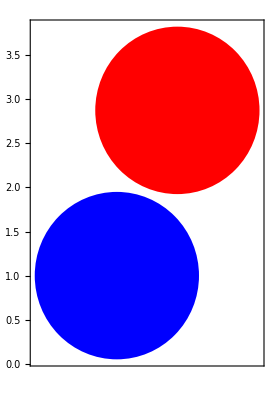

```mathematica
beeswarmPlot[dddd,Blend[{{Min[dddd],Blue},{Max[dddd],Red}},#]&/@dddd,
1,AspectRatio->Automatic]
```

### Do test calculation

```mathematica
(*test bistablePlot code*)
(*test LandauMaxLikelihood code*)
ageTest=15.(*10.*);
dataFullTest=Log[data[[Index[ageTest,ages]]]];
```

```mathematica
(*run max likelihood fitting*)
nuMax=1;
{fitMuTest,fitValsTest,fitVecsTest,fitParamsTest}=LandauMaxLikelihood[dataFullTest,nuMax];
```

```mathematica
(*2021/9/1 does maximum variance increase, too, on day 15?*)
```

```mathematica
(*day 1*)fitValsTest[[15]]
```

0.218628

```mathematica
(*day 3*)fitValsTest[[15]]
```

0.152617

```mathematica
(*day 6*)fitValsTest[[15]]
```

0.046758

```mathematica
3.13469×10^-12
```

```mathematica
(*day 10*)fitValsTest[[15]]
```

0.0555441

```mathematica
(*day 15 (yes, variance is largest on day 15)*)fitValsTest[[15]]
```

0.0354488

```mathematica
fitValsTest[[1]]
```

0.0354488

```mathematica
(*end 2021/9/1*)
```

```mathematica
(* from 2021/9/16, now with nuMu*)
fitParamsTest
```

{{-6.39428,{c→-6.08702,d→4.9494,nuMu→-1.08978}}}

```mathematica
seedRandom[1234];
bistablePlotEigvec[dataFullTest,fitMuTest,fitValsTest,fitVecsTest,fitParamsTest,1]
```

~/Dropbox (ASU)/Research/bees/geneExpression/Plots/220922_bistable_plot_along_eigvec__nuIndex1.pdf

```mathematica
seedRandom[1234];bistablePlotSingleGenes[dataFullTest,fitMuTest,fitValsTest,fitVecsTest,fitParamsTest,1]
```

NIntegrate::inumr: The integrand ⅇ^(0.-3.48406 («1»)^2+0.107889 eta^2-0.00155487 eta^4) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NMaxValue::cvmit: Failed to converge to the requested accuracy or precision within 1 iterations.

General::stop: Further output of NMaxValue::cvmit will be suppressed during this calculation.

{~/Dropbox (ASU)/Research/bees/geneExpression/Plots/220921_bistable_plot_single_gene__nuIndex1_1_vg.pdf,~/Dropbox (ASU)/Research/bees/geneExpression/Plots/220921_bistable_plot_single_gene__nuIndex1_2_hex 110.pdf,~/Dropbox (ASU)/Research/bees/geneExpression/Plots/220921_bistable_plot_single_gene__nuIndex1_3_P110.pdf,~/Dropbox (ASU)/Research/bees/geneExpression/Plots/220921_bistable_plot_single_gene__nuIndex1_4_transferrin 1.pdf,~/Dropbox (ASU)/Research/bees/geneExpression/Plots/220921_bistable_plot_single_gene__nuIndex1_5_LOC409966.pdf,~/Dropbox (ASU)/Research/bees/geneExpression/Plots/220921_bistable_plot_single_gene__nuIndex1_6_Hex70a.pdf,~/Dropbox (ASU)/Research/bees/geneExpression/Plots/220921_bistable_plot_single_gene__nuIndex1_7_JHE.pdf,~/Dropbox (ASU)/Research/bees/geneExpression/Plots/220921_bistable_plot_single_gene__nuIndex1_8_VG protein .pdf,~/Dropbox (ASU)/Research/bees/geneExpression/Plots/220921_bistable_plot_single_gene__nuIndex1_9_ilp1.pdf,~/Dropbox (ASU)/Research/bees/geneExpression/Plots/220921_bistable_plot_single_gene__nuIndex1_10_Def2.pdf}

### Automated analysis

```mathematica
(*run analysis across all days*)
```

```mathematica
landauAnalysis[age_,logData_,whitenData_,numNuMax_:10,BICthreshold_:0,dmin_:0.001,flipSignOfVecs_:True]:=
Block[
{dataFull,keptDimensions,keptBees,fitMu,fitVals,fitVecs,fitParams,bistableDimensions},

(*select data based on age*)
keptDimensions=If[age==4,90,91];
keptBees=If[age==4,nonBadBeesDayFour,allBees];

(*Optionally take the log*)
dataFull = If[logData,
Log[data[[Index[age,ages]]]],
data[[Index[age,ages]]]
][[keptBees,;;keptDimensions]];
(*Optionally whiten the data*)
If[whitenData,dataFull=Transpose[((#-Mean[#])/StandardDeviation[#])&/@Transpose[dataFull]];];

(*run maximum likelihood analysis*)
{fitMu,fitVals,fitVecs,fitParams}=LandauMaxLikelihood[dataFull,numNuMax,dmin,flipSignOfVecs];
(*find dimensions that meet the model selection criterion*)bistableDimensions=First/@Position[fitParams[[;;,1]],_?(#<-BICthreshold&)];
(*make plots and save to disk*)
bistablePlotEigvec[dataFull,fitMu,fitVals,fitVecs,fitParams,#,If[whitenData,"whitened",""]<>If[logData,"logData_day","day"]<>ToString[IntegerPart[age]]]&/@bistableDimensions;
bistablePlotSingleGenes[dataFull,fitMu,fitVals,fitVecs,fitParams,#,If[whitenData,"whitened",""]<>If[logData,"logData_day","day"]<>ToString[IntegerPart[age]]]&/@bistableDimensions
]
```

## make subplots for Figure 3 and Table 1

```mathematica
(*define threshold for likelihood ratio that we use to filter days --- for now just set at zero to not filter any days and we'll use python to deal with bayesian computations*)
```

```mathematica
With[{numNuMax=1,BICthreshold=0,dmin=0.001,(*Flip the sign of the eigenvector on selected days so that bees we expect to be out of the hive end up on the right side of the plots*)agesAndFlips={{1.,True},{3.,True},{4.,True},{6.,False},{10.,True},{15.,True}}},
SeedRandom[1234];
Table[
landauAnalysis[First[ageAndFlip],logData,whitenData,numNuMax,BICthreshold,dmin,Last[ageAndFlip]],
{ageAndFlip,agesAndFlips},
{logData,{True(*,False*)}},
{whitenData,{(*True,*)False}}
]
]
```

NIntegrate::inumr: The integrand ⅇ^(0.-0.980621 («1»)^2-0.0832239 eta^2-0.00105918 eta^4) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NMaxValue::cvmit: Failed to converge to the requested accuracy or precision within 1 iterations.

General::stop: Further output of NMaxValue::cvmit will be suppressed during this calculation.

{{{{{~/Dropbox (ASU)/Research/bees/geneExpression/Plots/220922_bistable_plot_single_gene_logData_day1_nuIndex1_1_hex 110.pdf}}}},{{{}}},{{{}}},{{{{~/Dropbox (ASU)/Research/bees/geneExpression/Plots/220922_bistable_plot_single_gene_logData_day6_nuIndex1_1_Hymenoptaecin.pdf,~/Dropbox (ASU)/Research/bees/geneExpression/Plots/220922_bistable_plot_single_gene_logData_day6_nuIndex1_2_JHE.pdf,~/Dropbox (ASU)/Research/bees/geneExpression/Plots/220922_bistable_plot_single_gene_logData_day6_nuIndex1_3_Def.pdf,~/Dropbox (ASU)/Research/bees/geneExpression/Plots/220922_bistable_plot_single_gene_logData_day6_nuIndex1_4_Malvolio.pdf,~/Dropbox (ASU)/Research/bees/geneExpression/Plots/220922_bistable_plot_single_gene_logData_day6_nuIndex1_5_Hex70a.pdf,~/Dropbox (ASU)/Research/bees/geneExpression/Plots/220922_bistable_plot_single_gene_logData_day6_nuIndex1_6_LOC406144.pdf,~/Dropbox (ASU)/Research/bees/geneExpression/Plots/220922_bistable_plot_single_gene_logData_day6_nuIndex1_7_vg.pdf}}}},{{{{~/Dropbox (ASU)/Research/bees/geneExpression/Plots/220922_bistable_plot_single_gene_logData_day10_nuIndex1_1_hex 110.pdf,~/Dropbox (ASU)/Research/bees/geneExpression/Plots/220922_bistable_plot_single_gene_logData_day10_nuIndex1_2_ilp1.pdf,~/Dropbox (ASU)/Research/bees/geneExpression/Plots/220922_bistable_plot_single_gene_logData_day10_nuIndex1_3_MRJP-3.pdf,~/Dropbox (ASU)/Research/bees/geneExpression/Plots/220922_bistable_plot_single_gene_logData_day10_nuIndex1_4_Hex70a.pdf,~/Dropbox (ASU)/Research/bees/geneExpression/Plots/220922_bistable_plot_single_gene_logData_day10_nuIndex1_5_Def2.pdf,~/Dropbox (ASU)/Research/bees/geneExpression/Plots/220922_bistable_plot_single_gene_logData_day10_nuIndex1_6_Malvolio.pdf,~/Dropbox (ASU)/Research/bees/geneExpression/Plots/220922_bistable_plot_single_gene_logData_day10_nuIndex1_7_vg.pdf,~/Dropbox (ASU)/Research/bees/geneExpression/Plots/220922_bistable_plot_single_gene_logData_day10_nuIndex1_8_P110.pdf,~/Dropbox (ASU)/Research/bees/geneExpression/Plots/220922_bistable_plot_single_gene_logData_day10_nuIndex1_9_LOC409966.pdf,~/Dropbox (ASU)/Research/bees/geneExpression/Plots/220922_bistable_plot_single_gene_logData_day10_nuIndex1_10_PRM1.pdf,~/Dropbox (ASU)/Research/bees/geneExpression/Plots/220922_bistable_plot_single_gene_logData_day10_nuIndex1_11_SVP NR2F1.pdf}}}},{{{{~/Dropbox (ASU)/Research/bees/geneExpression/Plots/220922_bistable_plot_single_gene_logData_day15_nuIndex1_1_vg.pdf,~/Dropbox (ASU)/Research/bees/geneExpression/Plots/220922_bistable_plot_single_gene_logData_day15_nuIndex1_2_hex 110.pdf,~/Dropbox (ASU)/Research/bees/geneExpression/Plots/220922_bistable_plot_single_gene_logData_day15_nuIndex1_3_P110.pdf,~/Dropbox (ASU)/Research/bees/geneExpression/Plots/220922_bistable_plot_single_gene_logData_day15_nuIndex1_4_transferrin 1.pdf,~/Dropbox (ASU)/Research/bees/geneExpression/Plots/220922_bistable_plot_single_gene_logData_day15_nuIndex1_5_LOC409966.pdf,~/Dropbox (ASU)/Research/bees/geneExpression/Plots/220922_bistable_plot_single_gene_logData_day15_nuIndex1_6_Hex70a.pdf,~/Dropbox (ASU)/Research/bees/geneExpression/Plots/220922_bistable_plot_single_gene_logData_day15_nuIndex1_7_JHE.pdf,~/Dropbox (ASU)/Research/bees/geneExpression/Plots/220922_bistable_plot_single_gene_logData_day15_nuIndex1_8_VG protein .pdf,~/Dropbox (ASU)/Research/bees/geneExpression/Plots/220922_bistable_plot_single_gene_logData_day15_nuIndex1_9_ilp1.pdf,~/Dropbox (ASU)/Research/bees/geneExpression/Plots/220922_bistable_plot_single_gene_logData_day15_nuIndex1_10_Def2.pdf}}}}}